```mathematica
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-r-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;

dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;



dHerf=Interpolation[Flatten[dHeru,1]];dEerf=Interpolation[Flatten[dEeru,1]];
```

```mathematica
dEerf[0.05,-1]
```

0.-8.8696 ⅈ

```mathematica
dHerf[0.05,-1]
```

0.+9.7317 ⅈ

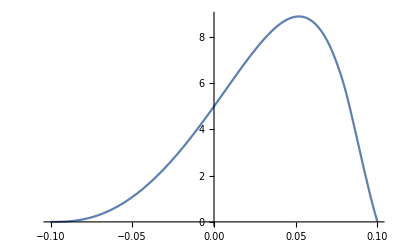

```mathematica
Plot[I*dEerf[x,-1],{x,-0.1,0.1}]
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-r-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];

Edgf=Interpolation[Flatten[Edgu,1]];
Eerf=Interpolation[Flatten[Eeru,1]];
```

```mathematica
Edau
```

0

```mathematica
Hdgf1[x_,t_]:=Chop[Hdgf[x,t],10^-7];
Herf1[x_,t_]:=Chop[Herf[x,t],10^-7];
Edgf1[x_,t_]:=Chop[Edgf[x,t],10^-7];
Eerf1[x_,t_]:=Chop[Eerf[x,t],10^-7];
dHerf1[x_,t_]:=Chop[dHerf[x,t],10^-7];
dEerf1[x_,t_]:=Chop[dEerf[x,t],10^-7];
```

```mathematica
Hdgfnu[x_,t_]:=Hdgf1[x,t];
Herfnu[x_,t_]:=Herf1[x,t]+dHerf1[x,t];
Edgfnu[x_,t_]:=Edgf1[x,t];
Eerfnu[x_,t_]:=Eerf1[x,t]+dEerf1[x,t];
```

```mathematica
(*kr图和a图此时应该一样，但是要不要考虑k介子的输入呢*)
```

```mathematica
(*pi+，u就是输入，d的话输入是dbar，所以要改一下*)
```

```mathematica
piCoe1=(1/(2*(2π)^4))*(-I);
```

```mathematica
pi1Hdgu[x_,t_]:=piCoe1*Hdgfnu[x,t];
pi1Heru[x_,t_]:=piCoe1*Herfnu[x,t];
pi1Edgu[x_,t_]:=piCoe1*Edgfnu[x,t];
pi1Eeru[x_,t_]:=piCoe1*Eerfnu[x,t];
```

```mathematica
pi1Hdgd[x_,t_]:=-piCoe1*Hdgfnu[-x,t];
pi1Herd[x_,t_]:=-piCoe1*Herfnu[-x,t];
pi1Edgd[x_,t_]:=-piCoe1*Edgfnu[-x,t];
pi1Eerd[x_,t_]:=-piCoe1*Eerfnu[-x,t];
```

```mathematica
(*pi0，ud都是输入，也都存在，两者完全一样*)
```

```mathematica
piCoe0=(1/(2*(2π)^4))*(-I);
```

```mathematica
pi0Hdguz[x_,t_]:=piCoe0*(1/2)*Hdgfnu[x,t];
pi0Heruz[x_,t_]:=piCoe0*(1/2)*Herfnu[x,t];
pi0Edguz[x_,t_]:=piCoe0*(1/2)*Edgfnu[x,t];
pi0Eeruz[x_,t_]:=piCoe0*(1/2)*Eerfnu[x,t];
```

```mathematica
pi0Hdguf[x_,t_]:=-piCoe0*(1/2)*Hdgfnu[-x,t];
pi0Heruf[x_,t_]:=-piCoe0*(1/2)*Herfnu[-x,t];
pi0Edguf[x_,t_]:=-piCoe0*(1/2)*Edgfnu[-x,t];
pi0Eeruf[x_,t_]:=-piCoe0*(1/2)*Eerfnu[-x,t];

pi0Heruall[x_,t_]:=pi0Heruf[x,t]+pi0Heruz[x,t];
pi0Eeruall[x_,t_]:=pi0Eeruf[x,t]+pi0Eeruz[x,t];
```

```mathematica
pi0Hdgdz[x_,t_]:=piCoe0*(1/2)*Hdgfnu[x,t];
pi0Herdz[x_,t_]:=piCoe0*(1/2)*Herfnu[x,t];
pi0Edgdz[x_,t_]:=piCoe0*(1/2)*Edgfnu[x,t];
pi0Eerdz[x_,t_]:=piCoe0*(1/2)*Eerfnu[x,t];
```

```mathematica
pi0Hdgdf[x_,t_]:=-piCoe0*(1/2)*Hdgfnu[-x,t];
pi0Herdf[x_,t_]:=-piCoe0*(1/2)*Herfnu[-x,t];
pi0Edgdf[x_,t_]:=-piCoe0*(1/2)*Edgfnu[-x,t];
pi0Eerdf[x_,t_]:=-piCoe0*(1/2)*Eerfnu[-x,t];

pi0Herdall[x_,t_]:=pi0Herdf[x,t]+pi0Herdz[x,t];
pi0Eerdall[x_,t_]:=pi0Eerdf[x,t]+pi0Eerdz[x,t];
```

```mathematica
(*pi-,ubar d *)
```

```mathematica
piCoe2=(1/(2*(2π)^4))*(-I);
```

```mathematica
pi2Hdgu[x_,t_]:=-piCoe2*Hdgfnu[-x,t];
pi2Heru[x_,t_]:=-piCoe2*Herfnu[-x,t];
pi2Edgu[x_,t_]:=-piCoe2*Edgfnu[-x,t];
pi2Eeru[x_,t_]:=-piCoe2*Eerfnu[-x,t];
```

```mathematica
pi2Hdgd[x_,t_]:=piCoe2*Hdgfnu[x,t];
pi2Herd[x_,t_]:=piCoe2*Herfnu[x,t];
pi2Edgd[x_,t_]:=piCoe2*Edgfnu[x,t];
pi2Eerd[x_,t_]:=piCoe2*Eerfnu[x,t];
```

```mathematica
(*K+ u sbar，和pi+一致*)
```

```mathematica
kCoe1=(1/(2*(2π)^4))*(-I);
```

```mathematica
k1Hdgu[x_,t_]:=kCoe1*Hdgfnu[x,t];
k1Heru[x_,t_]:=kCoe1*Herfnu[x,t];
k1Edgu[x_,t_]:=kCoe1*Edgfnu[x,t];
k1Eeru[x_,t_]:=kCoe1*Eerfnu[x,t];
```

```mathematica
k1Hdgs[x_,t_]:=-kCoe1*Hdgfnu[-x,t];
k1Hers[x_,t_]:=-kCoe1*Herfnu[-x,t];
k1Edgs[x_,t_]:=-kCoe1*Edgfnu[-x,t];
k1Eers[x_,t_]:=-kCoe1*Eerfnu[-x,t];
```

```mathematica
(*K0, d sbar，注意和pi0有区别*)
```

```mathematica
kCoe0=(1/(2*(2π)^4))*(-I);
```

```mathematica
k0Hdgd[x_,t_]:=kCoe0*Hdgfnu[x,t];
k0Herd[x_,t_]:=kCoe0*Herfnu[x,t];
k0Edgd[x_,t_]:=kCoe0*Edgfnu[x,t];
k0Eerd[x_,t_]:=kCoe0*Eerfnu[x,t];
```

```mathematica
k0Hdgs[x_,t_]:=-kCoe0*Hdgfnu[-x,t];
k0Hers[x_,t_]:=-kCoe0*Herfnu[-x,t];
k0Edgs[x_,t_]:=-kCoe0*Edgfnu[-x,t];
k0Eers[x_,t_]:=-kCoe0*Eerfnu[-x,t];
```